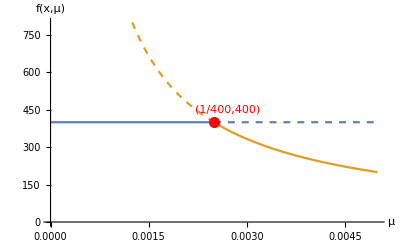

```mathematica
Show[
Plot[{400,1/m},{m,0,1/400},PlotRange->{{0,1/200},{0,800}},PlotStyle->{_,Dashed}],
Plot[{400,1/m},{m,1/400,1/200},PlotRange->{{0,1/200},{0,800}},PlotStyle->{Dashed,_}],
AxesLabel->{"μ","f(x,μ)"},
Epilog->{Red,PointSize[0.02],Point[{1/400,400}],Text["(1/400,400)",{1/370,450}]}
]
```

```mathematica
Solve[
{-dt r Sin[t]+dr Cos[t]==x,dt r Cos[t]+dr Sin[t]==y},{dt,dr}
]//FullSimplify
```

{{dt→1,dr→-6 m^3 r+11 m^2 r^3-6 m r^5+r^7}}

```mathematica
x=-r Sin[t]+r Cos[t](r^2-m)(r^2-2m)(r^2-3m);
y=r Cos[t]+r Sin[t](r^2-m)(r^2-2m)(r^2-3m);
```

```mathematica
Factor[-6 m^3 r+11 m^2 r^3-6 m r^5+r^7]
```

-r (m-r^2) (2 m-r^2) (3 m-r^2)

```mathematica
D[-6 m^3 r+11 m^2 r^3-6 m r^5+r^7,r]//Factor
```

-6 m^3+33 m^2 r^2-30 m r^4+7 r^6

```mathematica
D[-r (m-r^2) (2 m-r^2) (3 m-r^2),r]
```

2 r^2 (m-r^2) (2 m-r^2)+2 r^2 (m-r^2) (3 m-r^2)+2 r^2 (2 m-r^2) (3 m-r^2)-(m-r^2) (2 m-r^2) (3 m-r^2)

```mathematica
d=-6 m^3+33 m^2 r^2-30 m r^4+7 r^6
```

-6 m^3+33 m^2 r^2-30 m r^4+7 r^6

```mathematica
d/.{r->√(3m)}
```

12 m^3

```mathematica
Clear[x]
```

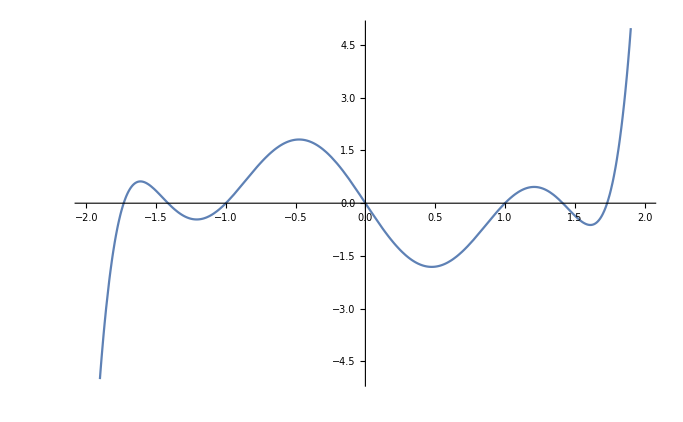

```mathematica
Plot[x(x^2-1)(x^2-2)(x^2-3),{x,-2,2},Ticks->None]
```

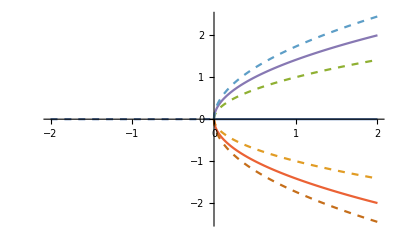

```mathematica
sol=Evaluate[{r}/.Solve[-r (m-r^2) (2 m-r^2) (3 m-r^2)==0,r]];
Show[
Plot[sol,{m,0,2},PlotRange->{{-2,2},All},PlotStyle->{_,Dashed,Dashed,_,_,Dashed,Dashed}],
Plot[sol,{m,-2,0},PlotStyle->Dashed]
]
```

```mathematica
{r}/.Solve[-r (m-r^2) (2 m-r^2) (3 m-r^2)==0,r]
```

{{0},{-√m},{√m},{-√2 √m},{√2 √m},{-√3 √m},{√3 √m}}

```mathematica
Clear[y]
```

```mathematica
Manipulate[
StreamPlot[{-y+x(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m),x+y(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m)},{x,-2,2},{y,-2,2},PlotLabel->m]
,{m,-2,2}]
```

```mathematica
Solve[√(3m)==2,m]
```

{{m→4/3}}

```mathematica
Grad[{-y+x(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m),x+y(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m)},{x,y}]/.{x->0,y->0}
```

{{-6 m^3,-1},{1,-6 m^3}}

```mathematica
Det[{{-6 m^3,-1},{1,-6 m^3}}-k IdentityMatrix[2]]//Factor
```

1+k^2+12 k m^3+36 m^6

```mathematica
Solve[1+k^2+12 k m^3+36 m^6==0,k]
```

{{k→-ⅈ-6 m^3},{k→ⅈ-6 m^3}}

```mathematica
Grad[{9y+x^3+x y,-x-m y+9y^2},{x,y}]
```

```mathematica
{{3 x^2+y,9+x},{-1,-m+18 y}}/.{x->0,y->0}
```

{{0,9},{-1,-m}}

```mathematica
Det[{{0,9},{-1,-m}}-k IdentityMatrix[2]]//Factor
```

9+k^2+k m

```mathematica
Solve[9+k^2+k m==0,k]
```

{{k→1/2 (-m-√(-36+m^2))},{k→1/2 (-m+√(-36+m^2))}}

```mathematica
px=9r Sin[t]+r^3 Cos[t]^3+r^2 Sin[t]Cos[t];
py=-r Cos[t]-m r Sin[t]+9r^2 Sin[t]^2;
Solve[
{-dt r Sin[t]+dr Cos[t]==px,dt r Cos[t]+dr Sin[t]==py},{dt,dr}
]//FullSimplify//Expand
```

{{dt→-Cos[t]^2-m Cos[t] Sin[t]-r^2 Cos[t]^3 Sin[t]-9 Sin[t]^2+8 r Cos[t] Sin[t]^2,dr→r^3 Cos[t]^4+8 r Cos[t] Sin[t]+r^2 Cos[t]^2 Sin[t]-m r Sin[t]^2+9 r^2 Sin[t]^3}}

```mathematica
NSolve[{9y+x^3+x y==0,-x+0.1y+9y^2==0},{x,y},Reals]
```

{{x→1.66976,y→-0.436322},{x→0.,y→0.}}

```mathematica
Manipulate[
StreamPlot[{9y+x^3+x y,-x-m y+9y^2},{x,-5,5},{y,-5,5},PlotLabel->m,StreamColorFunction->None,StreamPoints->{{{{0.3,0},Red},Automatic}}]
,{{m,0.5},-2,2}]
```

```mathematica
FourierTransform[Cos[x],x,s]
```

√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s]

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},StreamColorFunction->None,StreamPoints->{{{{1,0},Red},{{-1,-1},Green},Automatic}}]
```

```mathematica
Integrate[DiracDelta[-1+s],{s,-2,2}]
```

1

```mathematica
InverseFourierTransform[(√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s])Exp[-a^2 s^2 t],s,x]//FullSimplify
```

ⅇ^(-a^2 t) Cos[x]

```mathematica
InverseFourierTransform[f[s],s,x]
```

InverseFourierTransform[f[s],s,x]

```mathematica
Integrate[(√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s])Exp[-a^2 s^2 t]Exp[-I s x],{s,-Infinity,+Infinity}]
```

ⅇ^(-a^2 t) √(2 π) Cos[x]

```mathematica
(√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s])Exp[-a^2 s^2 t]Exp[-I s x]/.{{s->1},{s->-1}}
```

{ⅇ^(-a^2 t-ⅈ x) √(π/2) DiracDelta[0],ⅇ^(-a^2 t+ⅈ x) √(π/2) DiracDelta[0]}

```mathematica
Total[{ⅇ^(-a^2 t-ⅈ x) √(π/2) DiracDelta[0],ⅇ^(-a^2 t+ⅈ x) √(π/2) DiracDelta[0]}]//FullSimplify
```

```mathematica
ⅇ^(-a^2 t-ⅈ x) √(π/2) +ⅇ^(-a^2 t+ⅈ x) √(π/2) //FullSimplify
```

ⅇ^(-a^2 t) √(2 π) Cos[x]

```mathematica
Det[{{1-m,1},{1,-3-m}}]//Factor
```

-4+2 m+m^2

```mathematica
Eigensystem[{{1,1},{1,-3}}]
```

{{-1-√5,-1+√5},{{2-√5,1},{2+√5,1}}}

```mathematica
I
```

```mathematica
Normalize/@{{2-√5,1},{2+√5,1}}//FullSimplify
```

{{-√(1/2-1/(√5)),√(1/2+1/(√5))},{√(1/2+1/(√5)),1/(√(10+4 √5))}}

```mathematica
A={{1,1},{1,-3}}
```

{{1,1},{1,-3}}

```mathematica
A.{2-√5,1}
```

{3-√5,-1-√5}

```mathematica
(3-√5)/(2-√5)//FullSimplify
```

-1-√5

```mathematica
B={{-√(1/2-1/(√5)),√(1/2+1/(√5))},{√(1/2+1/(√5)),1/(√(10+4 √5))}}
```

{{-√(1/2-1/(√5)),√(1/2+1/(√5))},{√(1/2+1/(√5)),1/(√(10+4 √5))}}

```mathematica
B.A.Transpose@B//FullSimplify
```

{{-1-√5,0},{0,-1+√5}}

```mathematica
(-1+√5)/(-1-√5)//Simplify
```

1/2 (-3+√5)

```mathematica
1/8 D[(x+y)^2-(x-3y)^2,y]/.{y->0}
```

x

```mathematica
PolynomialQuotient[x^5+x^3,x^4+x+1,x]
```

x

```mathematica
PolynomialRemainder[x^5+x^3,x^4+x+1,x]
```

-x-x^2+x^3

```mathematica
(x^2+x+1)(x^5+x^3+1)+(x^2+x)(x^5+x^2+1)//Expand//.{a_Integer->Mod[a,2]}
```

```mathematica
1+2 x+2 x^2+2 x^3+2 x^4+2 x^5+2 x^6+2 x^7//.{a_Integer->Mod[a,2]}
```

1